```mathematica
eps=0.00005;
x01=0;
x02=3.5;
x03=-3.5;
δ=0.5;
```

```mathematica
(*1. Графики.*)
Print[Plot[{(x^3+Sin[x]+1)/12,x},{x,-0.1,0.1},AxesLabel->{x,y},PlotRange->{-0.1,0.1},PlotLabels->{"y = ϕ(x)","y = x"}],Plot[{(x^3+Sin[x]+1)/12,x},{x,-5,5},AxesLabel->{x,y},PlotRange->{-5,5},PlotLabels->{"y = ϕ(x)","y = x"}]];
```

-Graphics--Graphics-

```mathematica
{{n, Subscript[x, n], ϕ(Subscript[x, n])=(Subscript[x, n]^3+Sin[Subscript[x, n]]+1)/12}, {0, 0, 0.083333}, {1, 0.083333, 0.090318}, {2, 0.090318, 0.090911}, {3, 0.090911, 0.090961}, {4, 0.090961, 0.090966}}
```

```mathematica
Print[Plot[{√((12*x-Sin[x]-1)/x),x},{x,3.3,3.7},AxesLabel->{x,y},PlotRange->{3,4},PlotLabels->{"y = ϕ(x)","y = x"}],Plot[{√((12*x-Sin[x]-1)/x),x},{x,-5,5},AxesLabel->{x,y},PlotRange->{-5,5},PlotLabels->{"y = ϕ(x)","y = x"}]];
```

-Graphics--Graphics-

```mathematica
{{n, Subscript[x, n], ϕ(Subscript[x, n])=√((12*Subscript[x, n]-Sin[Subscript[x, n]]-1)/Subscript[x, n])}, {0, 3.5, 3.437224}, {1, 3.437224, 3.434214}, {2, 3.434214, 3.434066}, {3, 3.434066, 3.434059}}
```

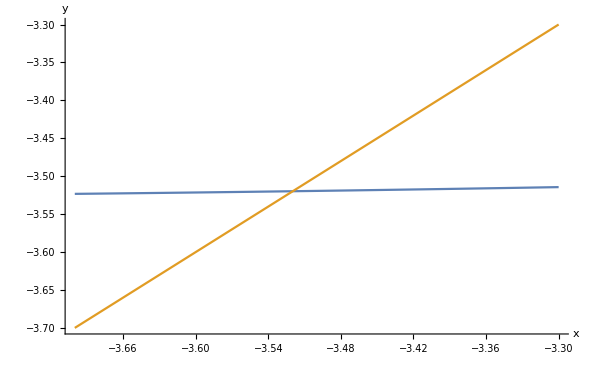
-Graphics--Graphics-

```mathematica
Print[Plot[{-√((12*x-Sin[x]-1)/x),x},{x,-3.3,-3.7},AxesLabel->{x,y},PlotRange->{-3,-4},PlotLabels->{"y = ϕ(x)","y = x"}],Plot[{-√((12*x-Sin[x]-1)/x),x},{x,-5,5},AxesLabel->{x,y},PlotRange->{-5,5},PlotLabels->{"y = ϕ(x)","y = x"}]];
```

```mathematica
{{n, Subscript[x, n], ϕ(Subscript[x, n])=-√((12*Subscript[x, n]-Sin[Subscript[x, n]]-1)/Subscript[x, n])}, {0, -3.5, -3.519366}, {1, -3.519366, -3.519794}, {2, -3.519794, -3.519803}}
```

```mathematica
(*2. Проверка условия теоремы.*)
fi1[x_]:=(x^3+Sin[x]+1)/12
fi2[x_]:=√((12*x-Sin[x]-1)/x)
fi3[x_]:=-√((12*x-Sin[x]-1)/x)
q1=Maximize[{D[fi1[x],x],-1≤x≤1},x][[1]]//N;
q2=Maximize[{D[fi2[x],x],3≤x≤4},x][[1]]//N;
q3=Maximize[{D[fi3[x],x],-4≤x≤-3},x][[1]]//N;
{{q1,q2,q3},{q1<1,q2<1,q3<1},{Abs[fi1[x01]-x01]<(1-q1)*δ,Abs[fi2[x02]-x02]<(1-q2)*δ,Abs[fi3[x03]-x03]<(1-q3)*δ}}
```

{{0.295025,0.0670022,0.03346},{True,True,True},{True,True,True}}

```mathematica
(*3. Корни уравнения.*)
Print["x_1 = ",xs[[1]],"; ","x_2 = ",xs[[2]],"; ","x_3 = ",xs[[3]]];
```

x_1 = 0.090966; x_2 = 3.43406; x_3 = -3.5198

```mathematica
(*4. Подстановка найденных корней в исходное уравнение.*)
Print[xs[[1]]^3+Sin[xs[[1]]]-12*xs[[1]]+1//N," ",xs[[2]]^3+Sin[xs[[2]]]-12*xs[[2]]+1//N," ",xs[[3]]^3+Sin[xs[[3]]]-12*xs[[3]]+1//N];
```

1.32411×10^-6 0.0000150725 8.20488×10^-6

```mathematica
{{n, Subscript[x, n], ϕ(Subscript[x, n])=(Subscript[x, n]^3+Sin[Subscript[x, n]]+1)/12}, {0, 0, 0.083333}, {1, 0.083333, 0.090318}, {2, 0.090318, 0.090911}, {3, 0.090911, 0.090961}, {4, 0.090961, 0.090966}}{{n, Subscript[x, n], ϕ(Subscript[x, n])=√((12*Subscript[x, n]-Sin[Subscript[x, n]]-1)/Subscript[x, n])}, {0, 3.5, 3.437224}, {1, 3.437224, 3.434214}, {2, 3.434214, 3.434066}, {3, 3.434066, 3.434059}}{{n, Subscript[x, n], ϕ(Subscript[x, n])=-√((12*Subscript[x, n]-Sin[Subscript[x, n]]-1)/Subscript[x, n])}, {0, -3.5, -3.519366}, {1, -3.519366, -3.519794}, {2, -3.519794, -3.519803}}
```

```mathematica
xs={0.090966,3.434059,-3.519803};
```

```mathematica
Print[Plot[{(x^3+Sin[x]+1)/12,x},{x,-5,5},AxesLabel->{x,y},PlotRange->{-5,5},PlotLabels->{"y = ϕ(x)","y = x"}]];
Print[Plot[{√((12*x-Sin[x]-1)/x),x},{x,-5,5},AxesLabel->{x,y},PlotRange->{-5,5},PlotLabels->{"y = ϕ(x)","y = x"}]];
Print[Plot[{-√((12*x-Sin[x]-1)/x),x},{x,-5,5},AxesLabel->{x,y},PlotRange->{-5,5},PlotLabels->{"y = ϕ(x)","y = x"}]];
```

-Graphics-

-Graphics-

-Graphics-